```mathematica
scape = Import["/Users/cwoodard/GitHub/oss-modeling/sugar_map.txt", "Table"];
```

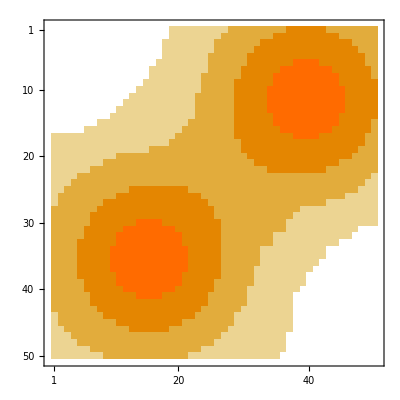

```mathematica
scape//MatrixPlot
```

```mathematica
shape = Dimensions[scape];
initAgents = 300;
initMaxSugar = 5;
shape[[1]]
randomInit = Table[{i,j},{i,shape[[1]]},{j,shape[[2]]}];
```

50

```mathematica
randomInit
```

{{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30},{1,31},{1,32},{1,33},{1,34},{1,35},{1,36},{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50}},48,{{50,1},{50,2},{50,3},{50,4},42,{50,47},{50,48},{50,49},{50,50}}}
 |  |  |  |

```mathematica
initScape=Map[{#,0}&,scape,{2}]
```

{{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0}},48,{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},34,{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}}
 |  |  |  |

```mathematica
scapeLookup[x_Integer,y_Integer]:=initScape[[x,y]]
scapeLookup[coord_List]:=scapeLookup[coord[[1]],coord[[2]]]
```

```mathematica
scapeLookup[13,18]
scapeLookup[{13,18}]
```

{1,0}

{1,0}

```mathematica
initScape//Dimensions
```

{50,50,2}

```mathematica
Dimensions[randomInit]
```

{50,50,2}

```mathematica
Flatten[randomInit,1]//Dimensions
```

{2500,2}

```mathematica
agentCoords=RandomSample[Flatten[randomInit,1],initAgents]
```

{{13,18},{40,47},{48,45},{10,22},{35,48},{16,48},{2,28},{18,47},{43,1},{10,47},{25,15},{15,1},{48,20},{13,24},{3,7},{50,8},{31,34},{36,20},{34,11},{46,28},{21,8},{46,21},{14,14},{44,27},{16,50},{3,46},{11,6},{43,15},{38,2},{41,13},{37,32},{29,21},{45,24},{40,37},{31,42},{4,7},{15,22},{22,27},{48,32},{29,34},{39,33},{23,28},{11,36},{9,8},{42,40},{34,42},{4,9},{22,28},{12,45},{21,41},{6,35},{42,32},{16,28},{40,44},{29,33},{14,22},{17,7},{40,48},{36,35},{4,21},{5,32},{13,47},{7,29},{35,43},{14,3},{7,18},{16,8},{2,50},{2,6},{49,50},{4,2},{28,4},{14,41},{48,21},{6,34},{10,5},{1,49},{4,40},{13,2},{25,41},{50,6},{42,25},{33,7},{22,19},{27,11},{10,49},{38,15},{16,14},{7,8},{26,9},{48,17},{10,9},{47,12},{2,29},{48,4},{23,41},{28,47},{13,9},{33,28},{12,4},{34,41},{19,38},{32,5},{50,46},{37,2},{39,45},{36,37},{33,41},{50,27},{49,31},{44,29},{47,30},{46,41},{4,22},{17,50},{9,11},{19,36},{2,27},{28,17},{4,32},{39,24},{29,31},{49,47},{21,50},{47,20},{19,46},{12,8},{34,37},{20,42},{38,21},{26,12},{25,14},{21,19},{5,34},{19,8},{34,48},{41,8},{49,15},{11,9},{26,13},{29,8},{37,43},{1,36},{18,20},{5,17},{30,10},{1,42},{24,22},{15,40},{44,24},{32,40},{50,31},{21,22},{33,25},{37,48},{38,16},{49,36},{4,31},{26,38},{2,24},{37,27},{37,24},{43,6},{36,24},{49,22},{33,50},{46,12},{2,3},{16,10},{48,39},{34,3},{32,7},{39,36},{17,20},{2,34},{37,28},{47,6},{8,11},{32,30},{35,50},{43,11},{42,16},{23,40},{9,44},{4,29},{29,41},{22,38},{30,44},{41,33},{17,40},{47,14},{41,12},{33,24},{26,33},{19,39},{15,37},{15,19},{40,40},{39,41},{31,5},{43,36},{36,7},{20,49},{39,27},{1,38},{23,33},{8,37},{7,14},{8,39},{28,21},{50,18},{30,25},{27,6},{10,31},{22,37},{16,17},{40,34},{23,11},{38,28},{39,14},{41,45},{3,9},{9,30},{11,25},{6,40},{17,49},{3,43},{3,13},{37,25},{12,29},{41,43},{42,11},{6,15},{42,12},{20,26},{3,32},{39,8},{10,45},{3,21},{9,22},{24,31},{36,34},{18,43},{34,7},{43,31},{45,42},{35,16},{42,21},{33,10},{6,24},{36,32},{1,23},{28,40},{45,49},{8,47},{41,44},{46,26},{6,14},{27,30},{15,9},{50,49},{9,26},{18,1},{21,3},{28,28},{26,17},{19,44},{18,16},{8,19},{25,28},{2,9},{48,23},{41,46},{36,18},{8,8},{12,25},{30,23},{13,37},{47,19},{37,3},{49,18},{9,17},{40,11},{39,28},{12,44},{15,4},{12,16},{13,13},{31,44},{29,24},{32,16},{15,26},{41,42},{34,39},{26,4},{34,18},{1,6},{47,37},{50,43},{35,37}}

```mathematica
agents=Append[#,RandomReal[initMaxSugar]]&/@agentCoords
```

{{13,18,0.0725935},{40,47,3.48442},{48,45,3.0671},{10,22,1.20304},{35,48,2.69693},{16,48,2.95659},{2,28,2.56131},{18,47,4.20806},{43,1,1.86144},{10,47,0.139229},{25,15,2.70998},{15,1,2.54944},{48,20,4.02594},{13,24,0.176445},{3,7,4.91703},{50,8,0.12873},{31,34,3.11076},{36,20,2.27105},{34,11,1.82106},{46,28,1.56778},{21,8,2.5099},{46,21,0.0798224},{14,14,1.7196},{44,27,1.46302},{16,50,0.94573},{3,46,0.34477},{11,6,3.35932},{43,15,2.85252},{38,2,3.78647},{41,13,2.47377},{37,32,0.720259},{29,21,0.327811},{45,24,3.79637},{40,37,3.26827},{31,42,2.52316},{4,7,1.19073},{15,22,3.81228},{22,27,4.88839},{48,32,1.74733},{29,34,2.19465},{39,33,2.41466},{23,28,2.12492},{11,36,0.40019},{9,8,3.27155},{42,40,1.12081},{34,42,4.49286},{4,9,0.287489},{22,28,1.83158},{12,45,0.762823},{21,41,0.471209},{6,35,0.570074},{42,32,0.743742},{16,28,1.94827},{40,44,1.68127},{29,33,0.54909},{14,22,0.447116},{17,7,4.03467},{40,48,4.95614},{36,35,3.25156},{4,21,1.99681},{5,32,3.99877},{13,47,1.71983},{7,29,3.1275},{35,43,0.769424},{14,3,1.92333},{7,18,1.50012},{16,8,1.33254},{2,50,1.91489},{2,6,2.8254},{49,50,0.175821},{4,2,0.872218},{28,4,4.37496},{14,41,4.1154},{48,21,2.65814},{6,34,2.85222},{10,5,2.31868},{1,49,0.788479},{4,40,4.69061},{13,2,1.82656},{25,41,2.22923},{50,6,4.90888},{42,25,4.89676},{33,7,1.35598},{22,19,1.31924},{27,11,4.32557},{10,49,3.59139},{38,15,0.188792},{16,14,1.20792},{7,8,0.250733},{26,9,1.20344},{48,17,4.02775},{10,9,0.0282473},{47,12,0.968248},{2,29,4.39118},{48,4,1.23727},{23,41,4.24257},{28,47,2.07583},{13,9,4.24456},{33,28,3.52185},{12,4,1.43848},{34,41,2.37762},{19,38,3.61573},{32,5,3.48087},{50,46,2.53589},{37,2,4.20068},{39,45,0.418959},{36,37,4.94088},{33,41,4.10949},{50,27,0.834347},{49,31,2.10424},{44,29,1.33195},{47,30,4.68145},{46,41,3.33759},{4,22,2.50423},{17,50,3.11083},{9,11,1.01965},{19,36,2.29286},{2,27,3.57703},{28,17,1.75318},{4,32,4.09179},{39,24,3.3979},{29,31,0.94061},{49,47,0.734875},{21,50,0.242489},{47,20,3.96758},{19,46,3.29006},{12,8,2.24389},{34,37,0.603694},{20,42,1.79284},{38,21,0.268622},{26,12,1.79929},{25,14,2.84337},{21,19,2.14364},{5,34,1.35944},{19,8,2.52014},{34,48,0.713682},{41,8,1.04025},{49,15,0.708046},{11,9,4.5795},{26,13,1.29079},{29,8,0.112621},{37,43,1.66751},{1,36,0.302877},{18,20,3.89226},{5,17,2.21816},{30,10,3.1447},{1,42,2.78554},{24,22,2.13686},{15,40,0.856202},{44,24,2.13033},{32,40,2.19986},{50,31,4.00179},{21,22,2.64817},{33,25,4.85486},{37,48,1.1496},{38,16,2.77249},{49,36,1.5376},{4,31,0.766321},{26,38,2.95631},{2,24,1.96787},{37,27,3.86952},{37,24,4.48081},{43,6,2.65209},{36,24,2.53685},{49,22,4.14144},{33,50,0.947937},{46,12,0.10989},{2,3,1.5977},{16,10,1.71277},{48,39,4.23653},{34,3,1.05775},{32,7,0.338434},{39,36,3.18441},{17,20,1.88438},{2,34,1.37576},{37,28,3.6048},{47,6,0.379256},{8,11,3.88666},{32,30,4.85227},{35,50,0.649246},{43,11,4.0842},{42,16,2.0247},{23,40,0.0504254},{9,44,3.43499},{4,29,3.07439},{29,41,4.51663},{22,38,0.0873588},{30,44,2.76872},{41,33,0.614915},{17,40,1.21158},{47,14,2.35546},{41,12,3.58069},{33,24,2.38846},{26,33,0.185625},{19,39,2.57578},{15,37,0.16046},{15,19,1.81512},{40,40,2.79194},{39,41,0.39444},{31,5,3.87387},{43,36,2.55736},{36,7,3.11112},{20,49,3.5034},{39,27,1.62621},{1,38,4.44225},{23,33,0.608501},{8,37,1.96178},{7,14,2.35406},{8,39,4.51519},{28,21,0.994},{50,18,1.25431},{30,25,0.272194},{27,6,1.77534},{10,31,0.652166},{22,37,4.78082},{16,17,1.34695},{40,34,0.192699},{23,11,1.52601},{38,28,4.71433},{39,14,3.22952},{41,45,4.69972},{3,9,0.982126},{9,30,4.82972},{11,25,1.5114},{6,40,4.71343},{17,49,3.9053},{3,43,3.80468},{3,13,4.98469},{37,25,3.92487},{12,29,2.03928},{41,43,2.85418},{42,11,2.58572},{6,15,4.19823},{42,12,0.309284},{20,26,0.952382},{3,32,3.22798},{39,8,1.6172},{10,45,4.98199},{3,21,3.65501},{9,22,1.86429},{24,31,1.39557},{36,34,1.52518},{18,43,4.75905},{34,7,1.23396},{43,31,4.68935},{45,42,3.62509},{35,16,2.46277},{42,21,1.41221},{33,10,0.564664},{6,24,2.64471},{36,32,0.113641},{1,23,1.234},{28,40,0.460558},{45,49,2.85222},{8,47,0.379123},{41,44,1.87016},{46,26,2.81372},{6,14,2.60663},{27,30,1.03193},{15,9,0.843265},{50,49,4.23599},{9,26,1.26789},{18,1,2.44962},{21,3,3.47905},{28,28,2.85772},{26,17,4.50793},{19,44,0.111378},{18,16,4.98901},{8,19,3.47052},{25,28,2.27798},{2,9,2.66309},{48,23,3.07484},{41,46,4.0353},{36,18,1.73766},{8,8,0.982607},{12,25,0.261986},{30,23,3.35338},{13,37,3.10179},{47,19,1.927},{37,3,4.85763},{49,18,0.905974},{9,17,1.29005},{40,11,3.77427},{39,28,1.41563},{12,44,0.0868775},{15,4,4.68854},{12,16,1.40374},{13,13,4.08847},{31,44,4.76843},{29,24,0.548253},{32,16,2.99537},{15,26,3.71386},{41,42,2.03319},{34,39,4.4447},{26,4,3.2954},{34,18,2.90285},{1,6,1.198},{47,37,2.62074},{50,43,4.31858},{35,37,0.53405}}

```mathematica
(*agent structure is {x_position, y_position, sugar_wealth}*)
agents = {}
Do[pos=RandomChoice[RandomChoice[randomInit]];
AppendTo[agents,AppendTo[pos, RandomReal[initMaxSugar]]];
  Delete[randomInit,pos];,
 initAgents];
```

{}

Delete::psl: Position specification 3.14767 in {{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30},{1,31},{1,32},{1,33},{1,34},{1,35},{1,36},{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50}},«48»,{{50,1},{50,2},{50,3},{50,4},{50,5},«40»,{50,46},{50,47},{50,48},{50,49},{50,50}}} is not a machine-sized integer or a list of machine-sized integers.

Delete::psl: Position specification 4.10159 in {{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30},{1,31},{1,32},{1,33},{1,34},{1,35},{1,36},{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50}},«48»,{{50,1},{50,2},{50,3},{50,4},{50,5},«40»,{50,46},{50,47},{50,48},{50,49},{50,50}}} is not a machine-sized integer or a list of machine-sized integers.

Delete::psl: Position specification 4.36125 in {{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30},{1,31},{1,32},{1,33},{1,34},{1,35},{1,36},{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50}},«48»,{{50,1},{50,2},{50,3},{50,4},{50,5},«40»,{50,46},{50,47},{50,48},{50,49},{50,50}}} is not a machine-sized integer or a list of machine-sized integers.

General::stop: Further output of Delete::psl will be suppressed during this calculation.

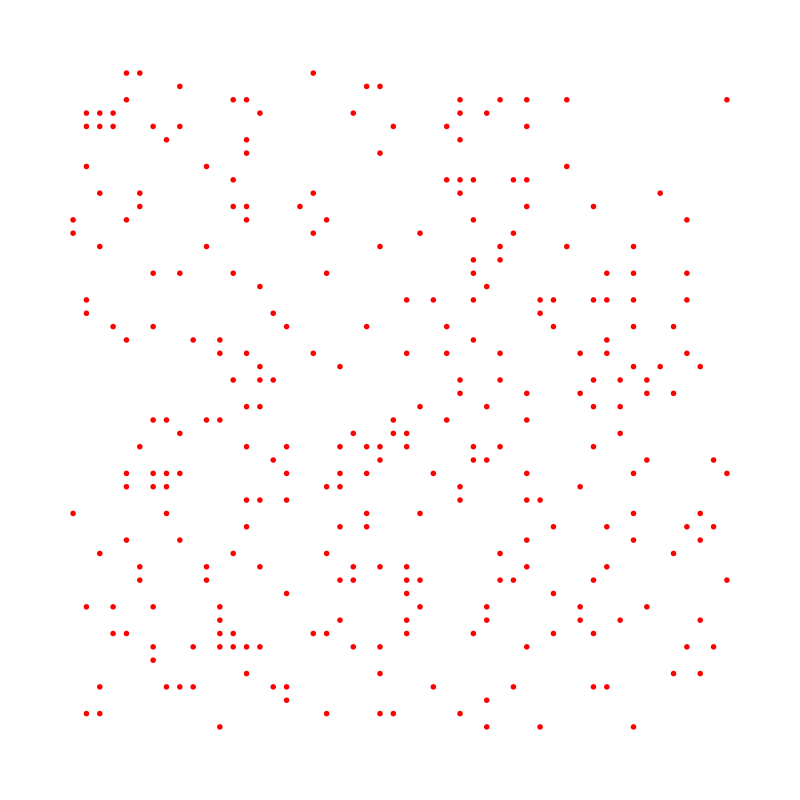

```mathematica
GraphicsGrid[Table[If[MemberQ[agents,{i,j,_}],Graphics[{Red,Disk[]}], ],{i,shape[[1]]},{j,shape[[2]]}], ImageSize->800]
```

```mathematica
(*change agent's coordinates from loc to dest, gain any sugar at dest, 
AgentMove[{loc,dest},
```